Программа состоит из 5 методов.
1) DispersionPlot по параметрам α, γ, β (см. пдф файл) строит графики дисперсии.
2) ScatteringSolutionNormal находит коэффициенты сшивки при нормальном падении света слева направо. 
На вход принимает [k0, α, γ, β, {fp,fm}]=[энергия, материальные параметры α, γ, β, {пара чисел, сумма квадратов модулей которых равна 1 } ]. Последняя пара аргументов определяет поляризацию падающей волны {1,0} - правая поляризация, {0,1} - левая.  
Возвращает список { } длины 9, у которого первые 1 и 2 аргументы коэффициенты прохождения и отражения,3 и 4 степень круговой поляризации прошедшей и отраженной волн, 5 и 6 первый стокс,7 и 8 второй стокс, 9- список собственных частот, 10 список амплитуд при соответствующих поляризациях отраженной и прошедших волн
3) GetPlotsNormal строит серию графиков по энергии используя методы выше. Т.е. это основной метод которой придется вызывать.
На вход принимает [{α, γ, β}, {fp,fm}, {k0min, k0max, k0step}] --[{3 материальных параметра}, {2 параметра характеризующих падающую поляризацию}, {3 параметра - границы построения графиков и шаг} ].
4) ScatteringSolutionParaxial находит коэффициенты сшивки при падении под малым углом. 
На вход принимает [{k0, np, ϕ} ,{α, γ, β}, {fp, fm}, {r, B ,e3 }] [{энергия, перпендикулярную долю волнового вектора, полярный угол волнового вектора}, {3 основных материальных параметра}, { падающую поляризацию- 2 аргумента}, {дополнительные три материальных параметра, которые появляются в поправках, см пдф файл}]. 
Вывод аналогичен ScatteringSolutionNormal.
5) GetPlotsParaxial строит графики по энергии при наклонном падении. 
Ввод в формате [{np, ϕ }, {α, γ, β}, {fp,fm}, {r, B, e3}, {k0min, k0max, k0step}] обозначения те же что и выше.

```mathematica
q=1;L=100;
```

```mathematica
DispersionPlot[α_,γ_,β_]:=Module[{r},
r=Manipulate[Plot[{Sqrt[(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)],Sqrt[(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)]},{n,d+1-m,d+1+m},AxesLabel->{"p_3/q","k_0/q"} ,GridLines -> Automatic,PlotLabel->{"Закон дисперсии"}],{m,20,0},{d,0,10}];
r];
```

```mathematica
ScatteringSolutionNormal[k0_,α_,γ_,β_,in_]:=Module[{m31,m32,m33,m34,bl,hp,hm,xl,xr,gg,b,res,trans,ref,xi1Trans,xi3Trans,xi1Ref,xi3Ref,xi2Trans,xi2Ref},
bl={in[[1]],in[[2]],hp,hm};
gg=xr/Sqrt[2]{0,2,0,k0/q 2}+xl/Sqrt[2]{2,0,k0/q 2,0};
f[s_,θ_,ϕ_]:={Cos[ϕ]Cos[θ]-ⅈ s Sin[ϕ],Sin[ϕ]Cos[θ]+ⅈ s Cos[ϕ],-Sin[θ]}1/(√2);
{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ),n];
U[z_]:={{(β k0^2)/(q^2 m31^2-α k0^2)ⅇ^(ⅈ m31 q z),(β k0^2)/(q^2 m32^2-α k0^2)ⅇ^(ⅈ m32 q z),(β k0^2)/(q^2 m33^2-α k0^2)ⅇ^(ⅈ m33 q z),(β k0^2)/(q^2 m34^2-α k0^2)ⅇ^(ⅈ m34 q z)},
{ⅇ^(ⅈ (m31-2) q z),ⅇ^(ⅈ (m32-2) q z),ⅇ^(ⅈ (m33-2) q z),ⅇ^(ⅈ (m34-2) q z)},
{m31  ⅇ^(ⅈ m31 q z)(β k0^2)/(q^2 m31^2-α k0^2),m32  ⅇ^(ⅈ m32 q z) (β k0^2)/(q^2 m32^2-α k0^2),m33  ⅇ^(ⅈ m33 q z) (β k0^2)/(q^2 m33^2-α k0^2),m34  ⅇ^(ⅈ m34 q z) (β k0^2)/(q^2 m34^2-α k0^2)},
{ⅇ^(ⅈ (m31-2) q z)(m31-2),ⅇ^(ⅈ (m32-2) q z)(m32-2),ⅇ^(ⅈ (m33-2) q z)(m33-2),ⅇ^(ⅈ (m34-2) q z)(m34-2)}};
U0=1/Sqrt[2]{{0,2,-2,0},{2,0,0,-2},{0,2 k0/q,2 k0/q,0},{2 k0/q,0,0,2 k0/q}};
T={{ⅇ^(-ⅈ k0 L),0,0,0},{0,ⅇ^(-ⅈ k0 L),0,0},{0,0,ⅇ^(-ⅈ k0 L),0},{0,0,0,ⅇ^(-ⅈ k0 L)}};
b=Inverse[U[-L]].U0.T.bl;
res={xl,xr,hp,hm}/.Solve[U[0].b==gg,{hp,hm,xl,xr}];
{xl,xr,hp,hm}={res[[1]][[1]],res[[1]][[2]],res[[1]][[3]],res[[1]][[4]]};
trans=(Abs[xl]^2+Abs[xr]^2)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
ref = (Abs[hp]^2+Abs[hm]^2)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
xi2Trans=(Abs[xr]^2-Abs[xl]^2)/(Abs[xl]^2+Abs[xr]^2);
xi1Trans=(xl*Conjugate[xr]-Conjugate[xl]*xr)/(ⅈ(Abs[xl]^2+Abs[xr]^2));
xi3Trans=(xl*Conjugate[xr]+Conjugate[xl]*xr)/(Abs[xl]^2+Abs[xr]^2);
xi2Ref=(Abs[hp]^2-Abs[hm]^2)/(Abs[hp]^2+Abs[hm]^2);
xi1Ref=(hm*Conjugate[hp]-Conjugate[hm]*hp)/(ⅈ(Abs[hm]^2+Abs[hp]^2));
xi3Ref=(hm*Conjugate[hp]-Conjugate[hm]*hp)/(ⅈ(Abs[hm]^2+Abs[hp]^2));

{trans,ref,xi2Trans,xi2Ref,xi1Trans,xi1Ref,xi3Trans,xi3Ref,{m31,m32,m33,m34},{xl,xr,hp,hm}}](*1 и 2 коэффициенты прохождения и отражения,3 и 4 степень круговой поляризации прошедшей и отраженной волн, 5 и 6 первый стокс,7 и 8 второй стокс, 9- список собственных частот,10 список амплитуд при соответствующих поляризациях отраженной и прошедших волн, *)
```

```mathematica
GetPlotsNormal[{α_,γ_,β_},inPol_,{k0min_,k0max_,k0step_}]:=Module[{r,xi1Tr,xi2Tr,xi3Tr,xi1Ref,xi2Ref,xi3Ref},

calc=ParallelTable[{k0,ScatteringSolutionNormal[k0,α,γ,β,{inPol[[1]],inPol[[2]]}]},{k0,k0min,k0max,k0step}];
tp=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[1]]},{i,1,1+(k0max-k0min)/k0step}];(*коэфициент прохождения*)
xi2Tr=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[3]]},{i,1,1+(k0max-k0min)/k0step}];(*степень круговой поляризации прошедшей волны (второй стокс) *)
xi1Tr=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[5]]},{i,1,1+(k0max-k0min)/k0step}];(*первый стокс прошедшей волны *)
xi3Tr=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[7]]},{i,1,1+(k0max-k0min)/k0step}];(*третий стокс прошедшей волны*)
tpR=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[2]]},{i,1,1+(k0max-k0min)/k0step}];(*коэфициент отражения*)
xi2Ref=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[4]]},{i,1,1+(k0max-k0min)/k0step}];(*степень круговой поляризации отраженной (второй стокс)*)
xi1Ref=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[6]]},{i,1,1+(k0max-k0min)/k0step}];(*первый стокс отраженной волны *)
xi3Ref=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[8]]},{i,1,1+(k0max-k0min)/k0step}];(*третий стокс отраженной волны*)
Print["Материальные параметры: α=",α,", γ=",γ,", β=",β];
Print["Поляризация падающей волны: ","(правая)d+=",inPol[[1]],"; (левая)d-=",inPol[[2]]];
r={
{
ListLinePlot[tp,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"Коэф. прохождения"],
ListLinePlot[{xi1Tr,xi2Tr,xi3Tr},AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLegends->{"1 Стокс пр", "2 Стокс пр", "3 Стокс пр"}],
ListLinePlot[xi1Tr,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"1 Стокс пр. волны"],
ListLinePlot[xi2Tr,AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLabel->"Ст. поляр. пр. волны",PlotStyle->Orange],
ListLinePlot[xi3Tr,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"3 Стокс пр. волны",PlotStyle->Green]
},
{
(*ListLinePlot[{tpR,xi2Ref},PlotRange->All,AxesLabel-> {"k_0/q",None},PlotStyle-> {Red,Gray},PlotLegends->{"Коэффициент отражения" ,"степень круговой поляризации
отраженной волны"}],*)
ListLinePlot[tpR,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotStyle-> Red,PlotLabel->"Коэф.отражения"],
ListLinePlot[{xi1Ref,xi2Ref,xi3Ref},AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLegends->{"1 Стокс отр", "2 Стокс отр", "3 Стокс отр"}],
ListLinePlot[xi1Ref,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"1 Стокс отр. волны"],
ListLinePlot[xi2Ref,AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLabel->"Ст. поляр. отр. волны",PlotStyle->Orange],
ListLinePlot[xi3Ref,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"3 Стокс отр. волны",PlotStyle->Green]
},
DispersionPlot[α,γ,β]
}

]
```

```mathematica
GetPlotsParaxial[{np_,ϕ_},{α_,γ_,β_},inPol_,{r_,B_,e3_},{k0min_,k0max_,k0step_}]:=Module[{res},

calc=ParallelTable[{k0,ScatteringSolutionParaxial[{k0,np,ϕ},{α,γ,β},{inPol[[1]],inPol[[2]]},{r,B,e3}]},{k0,k0min,k0max,k0step}];
tp=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[5]]},{i,1,1+(k0max-k0min)/k0step}];(*коэфициент прохождения*)
tpdeg=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[7]]},{i,1,1+(k0max-k0min)/k0step}];(*степень круговой поляризации прошедшей *)
tpR=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[6]]},{i,1,1+(k0max-k0min)/k0step}];(*коэфициент прохождения*)
tpdegR=ParallelTable[{calc[[i]][[1]],calc[[i]][[2]][[8]]},{i,1,1+(k0max-k0min)/k0step}];(*степень круговой поляризации отраженной*)
Print["Материальные параметры: α=",α,", γ=",γ,", β=",β];
Print["Поляризация падающей волны: ","(правая)d+=",inPol[[1]],"; (левая)d-=",inPol[[2]]];
res={{ListLinePlot[{tp,tpdeg},PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLegends->{"Коэффициент прохождения" ,"степень поляризации
прошедшей волны"}],
ListLinePlot[tp,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"Коэф. прохождения"],
ListLinePlot[tpdeg,PlotStyle->Orange,AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLabel->"Ст. поляр. пр. волны"]},
{ListLinePlot[{tpR,tpdegR},PlotRange->All,AxesLabel-> {"k_0/q",None},PlotStyle-> {Red,Gray},PlotLegends->{"Коэффициент отражения" ,"степень поляризации
отраженной волны"}],
ListLinePlot[tpR,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotStyle-> Red,PlotLabel->"Коэф.отражения"],ListLinePlot[tpdegR,PlotStyle->Gray,AxesLabel-> {"k_0/q",None},PlotRange->All,PlotLabel->"Ст. поляр. отр. волны"]},
DispersionPlot[α,γ,β]}

]
```

```mathematica
ScatteringSolutionParaxial[{k0_,np_,ϕ_},{α_,γ_,β_},in_,{r_,B_,e3_}]:=Module[{m31,m32,m33,m34,τ,kp,k3,n3,Λ,βc,rc,Bc,bl,b,hp,hm,gg,tp,tm,trans,ref,polDegTrans,polDegRef,res,tp0,tm0,hp0,hm0,b10,b20,b30,b40,tp1,tm1,hp1,hm1,b11,b21,b31,b41,res0,res1,Itp,Itm,Ihp,Ihm},
τ=q^2/k0^2;
kp=k0 np;
Λ=1/(k0^2 e3);
βc = Conjugate[β];
rc=Conjugate[r];
Bc=Conjugate[B];
k3=Sqrt[k0^2-0];
n3=k3/k0;
g[s_]:={1-s,1+s,k0/q(1-s ),k0/q(1+s )};
bl0={in[[1]],in[[2]],hp0,hm0};
bl1={0,0,hp1,hm1};
gg0=tp0/Sqrt[2] g[1]+tm0/Sqrt[2] g[-1];
gg1=tp1/Sqrt[2] g[1]+tm1/Sqrt[2] g[-1];
{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ),n];
{ap0[n_],amm2[n_],ap1[n_],amm1[n_],apm1[n_],amm3[n_]}:={1,(-α+n^2 τ)/β,(ⅇ^(-ⅈ (r+rc)) kp q Λ (B ⅇ^(ⅈ rc) ((-1+n) β+ⅇ^(2 ⅈ r) (1+n) (-γ+(-1+n)^2 τ))+Bc ⅇ^(ⅈ r) ((-2+n) β+ⅇ^(2 ⅈ rc) n (-α+n^2 τ))))/(2 (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),(ⅇ^(-ⅈ (r+rc)) kp q Λ (Bc ⅇ^(ⅈ r) (-α+(1+n)^2 τ) ((-2+n) β+ⅇ^(2 ⅈ rc) n (-α+n^2 τ))+B ⅇ^(ⅈ rc) β (α-n α+(1+n) (ⅇ^(2 ⅈ r) βc+(-1+n^2) τ))))/(2 β (β βc+(-γ+(-1+n)^2 τ) (α-(1+n)^2 τ))),(ⅇ^(-ⅈ (r+rc)) kp q Λ (B ⅇ^(ⅈ rc) (-α+n^2 τ) ((-3+n) β+ⅇ^(2 ⅈ r) (-1+n) (-γ+(-3+n)^2 τ))+Bc ⅇ^(ⅈ r) (-γ+(-3+n)^2 τ) ((-2+n) β+ⅇ^(2 ⅈ rc) n (-α+n^2 τ))))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ))),(ⅇ^(-ⅈ (r+rc)) kp q Λ (B ⅇ^(ⅈ rc) (α-n^2 τ) (-ⅇ^(2 ⅈ r) (-1+n) βc+(-3+n) (α-(-1+n)^2 τ))+Bc ⅇ^(ⅈ r) βc ((-2+n) β+ⅇ^(2 ⅈ rc) n (-α+n^2 τ))))/(2 β (β βc+(-γ+(-3+n)^2 τ) (α-(-1+n)^2 τ)))};
ψp0[m3_,z_]:=ap0[m3] ⅇ^(ⅈ(m3+0)(q z-ϕ)+ⅈ ϕ);
ψp1[m3_,z_]:=+ap1[m3] ⅇ^(ⅈ(m3+1)(q z-ϕ)+ⅈ ϕ)+apm1[m3] ⅇ^(ⅈ(m3-1)(q z-ϕ)+ⅈ ϕ);
ψm0[m3_,z_]:=amm2[m3] ⅇ^(ⅈ(m3-2)(q z-ϕ)-ⅈ ϕ);
ψm1[m3_,z_]:=amm1[m3] ⅇ^(ⅈ(m3-1)(q z-ϕ)-ⅈ ϕ)+amm3[m3] ⅇ^(ⅈ(m3-3)(q z-ϕ)-ⅈ ϕ);
ψ30[m3_,z_]=(Λ(-Bc k0^2(ⅇ^(-ⅈ(q z-ϕ+rc))ψp0[m3,z]+ⅇ^(ⅈ(q z-ϕ+rc))ψm0[m3,z])))/2;
ψ31[m3_,z_]=(Λ(ⅈ kp D[ψp0[m3,z]+ψm0[m3,z],z]-Bc k0^2(ⅇ^(-ⅈ(q z-ϕ+rc))ψp1[m3,z]+ⅇ^(ⅈ(q z-ϕ+rc))ψm1[m3,z])))/2;
rotψp0[m3_,z_]=-ⅈ/q(ⅇ^(-ⅈ ϕ)D[ψp0[m3,z],z]);
rotψp1[m3_,z_]=-ⅈ/q(ⅇ^(-ⅈ ϕ)D[ψp1[m3,z],z]-ⅈ kp ψ30[m3,z]);
rotψm0[m3_,z_]=-ⅈ/q(ⅇ^(ⅈ ϕ)D[ψm0[m3,z],z]);
rotψm1[m3_,z_]=-ⅈ/q(ⅇ^(ⅈ ϕ)D[ψm1[m3,z],z]-ⅈ kp ψ30[m3,z]);
Uz0[z_]:={{ⅇ^(-ⅈ ϕ)ψp0[m31,z],ⅇ^(-ⅈ ϕ)ψp0[m32,z],ⅇ^(-ⅈ ϕ)ψp0[m33,z],ⅇ^(-ⅈ ϕ)ψp0[m34,z]},{ⅇ^(ⅈ ϕ)ψm0[m31,z],ⅇ^(ⅈ ϕ)ψm0[m32,z],ⅇ^(ⅈ ϕ)ψm0[m33,z],ⅇ^(ⅈ ϕ)ψm0[m34,z]},
{rotψp0[m31,z],rotψp0[m32,z],rotψp0[m33,z],rotψp0[m34,z]},{rotψm0[m31,z],rotψm0[m32,z],rotψm0[m33,z],rotψm0[m34,z]} };
Uz1[z_]:={{ⅇ^(-ⅈ ϕ)ψp1[m31,z],ⅇ^(-ⅈ ϕ)ψp1[m32,z],ⅇ^(-ⅈ ϕ)ψp1[m33,z],ⅇ^(-ⅈ ϕ)ψp1[m34,z]},{ⅇ^(ⅈ ϕ)ψm1[m31,z],ⅇ^(ⅈ ϕ)ψm1[m32,z],ⅇ^(ⅈ ϕ)ψm1[m33,z],ⅇ^(ⅈ ϕ)ψm1[m34,z]},
{rotψp1[m31,z],rotψp1[m32,z],rotψp1[m33,z],rotψp1[m34,z]},{rotψm1[m31,z],rotψm1[m32,z],rotψm1[m33,z],rotψm1[m34,z]} };
U0=1/Sqrt[2]{{n3-1,n3+1,-n3-1,-n3+1},{n3+1,n3-1,-n3+1,-n3-1},{k0/q(1-n3),k0/q(1+n3),k0/q(1+n3),k0/q(1-n3)},{k0/q(1+n3),k0/q(1-n3),k0/q(1-n3),k0/q(1+n3)}};
T={{ⅇ^(-ⅈ k3 L),0,0,0},{0,ⅇ^(-ⅈ k3 L),0,0},{0,0,ⅇ^(ⅈ k3 L),0},{0,0,0,ⅇ^(ⅈ k3 L)}};

res0={tp0,tm0,hp0,hm0,b10,b20,b30,b40}/.Solve[{Uz0[0].{b10,b20,b30,b40}==gg0,Uz0[-L].{b10,b20,b30,b40}==U0.T.bl0},{hp0,hm0,tp0,tm0,b10,b20,b30,b40}];
{tp0,tm0,hp0,hm0,b10,b20,b30,b40}={res0[[1]][[1]],res0[[1]][[2]],res0[[1]][[3]],res0[[1]][[4]],res0[[1]][[5]],res0[[1]][[6]],res0[[1]][[7]],res0[[1]][[8]]};

res1={tp1,tm1,hp1,hm1,b11,b21,b31,b41}/.Solve[{Uz1[0].{b10,b20,b30,b40}+Uz0[0].{b11,b21,b31,b41}==gg1,Uz1[-L].{b10,b20,b30,b40}+Uz0[-L].{b11,b21,b31,b41}==U0.T.bl1},{hp1,hm1,tp1,tm1,b11,b21,b31,b41}];
{tp1,tm1,hp1,hm1,b11,b21,b31,b41}={res1[[1]][[1]],res1[[1]][[2]],res1[[1]][[3]],res1[[1]][[4]],res1[[1]][[5]],res1[[1]][[6]],res1[[1]][[7]],res1[[1]][[8]]};

{tp,tm,hp,hm}={tp0+np tp1,tm0+np tm1,hp0+np hp1,hm0+np hm1};

(*trans=(Abs[tp]^2+Abs[tm]^2)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
ref = (Abs[hp]^2+Abs[hm]^2)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
polDegTrans=(Abs[tp]^2-Abs[tm]^2)/(Abs[tp]^2+Abs[tm]^2);
polDegRef=(Abs[hp]^2-Abs[hm]^2)/(Abs[hp]^2+Abs[hm]^2);*)


Itp=Abs[tp0]^2+np(tp0 Conjugate[tp1]+tp1 Conjugate[tp0])(*+np^2Abs[tp1]*);
Itm=Abs[tm0]^2+np(tm0 Conjugate[tm1]+tm1 Conjugate[tm0])(*+np^2Abs[tm1]*);
Ihp=Abs[hp0]^2+np(hp0 Conjugate[hp1]+hp1 Conjugate[hp0]);
Ihm=Abs[hm0]^2+np(hm0 Conjugate[hm1]+hm1 Conjugate[hm0]);
trans=(Itp+Itm)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
ref = (Ihp+Ihm)/(Abs[in[[1]]]^2+Abs[in[[2]]]^2);
polDegTrans=((Itp-Itm)/(Abs[tp0]^2+Abs[tm0]^2)-((Abs[tp0]^2-Abs[tm0]^2)np(tp0 Conjugate[tp1]+tp1 Conjugate[tp0]+tm0 Conjugate[tm1]+tm1 Conjugate[tm0]))/((Abs[tp0]^2+Abs[tm0]^2)^2));(*(Itp-Itm)/(Itp+Itm);*)
polDegRef=(Ihp-Ihm)/(Abs[hp0]^2+Abs[hm0]^2)-((Abs[hp0]^2-Abs[hm0]^2)np(hp0 Conjugate[hp1]+hp1 Conjugate[hp0]+hm0 Conjugate[hm1]+hm1 Conjugate[hm0]))/((Abs[hp0]^2+Abs[hm0]^2)^2);(*(Ihp-Ihm)/(Ihp+Ihm);*)

{tp,tm,hp,hm,trans,ref,polDegTrans,polDegRef,{m31,m32,m33,m34}}



]
```

Случай холестериков. Левая поляризация почти полностью отражается от щели, для правой среда прозрачна в оптике (0.1-5). При больших энергиях поляризация осциллирует. Известные результаты.

Материальные параметры: α=1, γ=1, β=0.1

Поляризация падающей волны: (правая)d+=0; (левая)d-=1

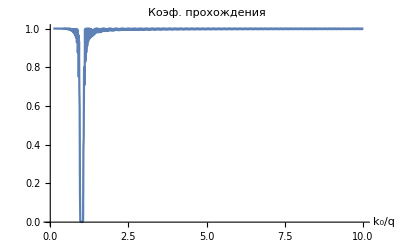
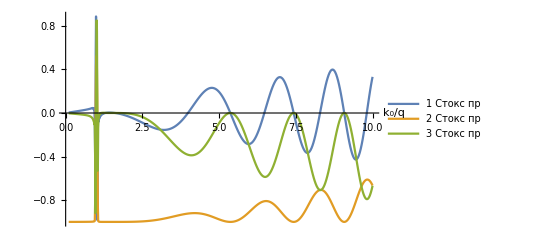
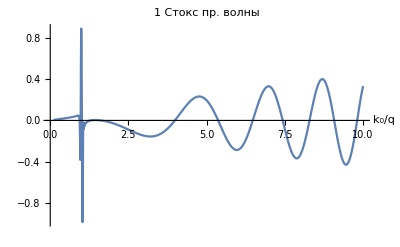
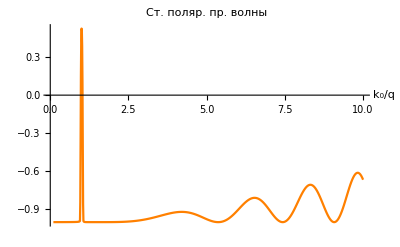
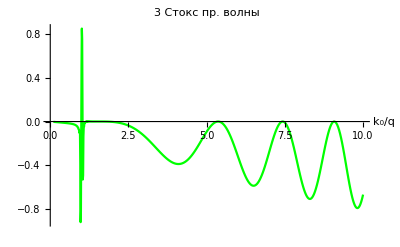
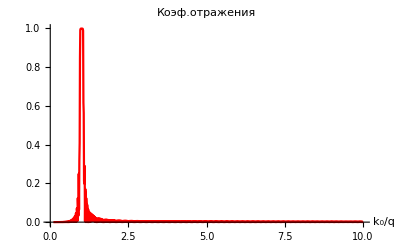
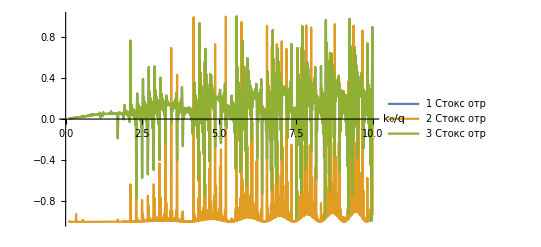
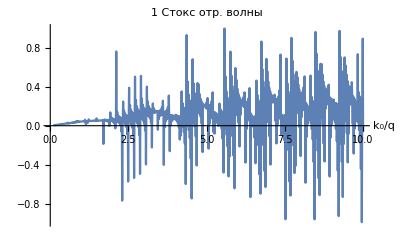

```mathematica
GetPlotsNormal[{1,1,0.1},{0,1},{0.1,10,0.01}]
```

При падении правополяризованного света, как и в случае холестерика,  первая щель не ощущается, но зато можно пронаблюдать вторую щель (Так можно отличать холестерика от нашей среды). От второй щели отражается меньше, чем в областях вне нее. Но отражается с чисто левой поляризацией. Прошедший свет в окрестности щели несет эллиптическую поляризацию и плоскую в центре щели.

Материальные параметры: α=1, γ=0.5, β=0.01

Поляризация падающей волны: (правая)d+=1; (левая)d-=0

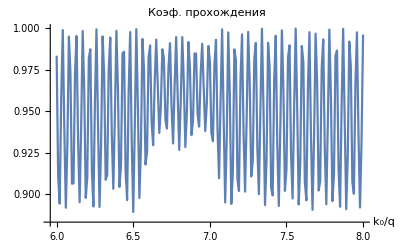
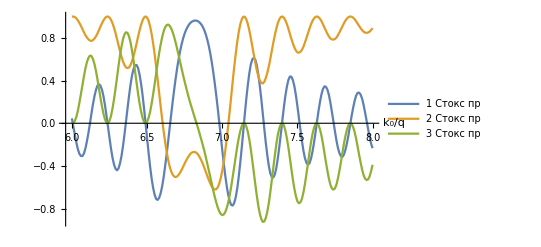
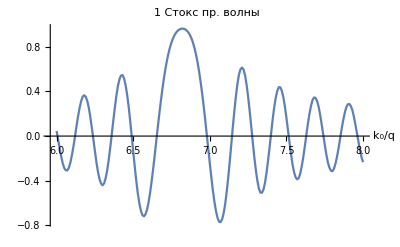
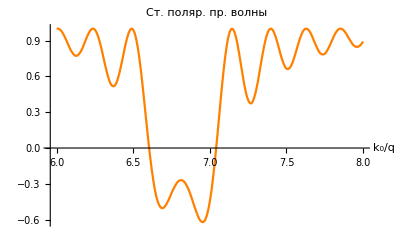
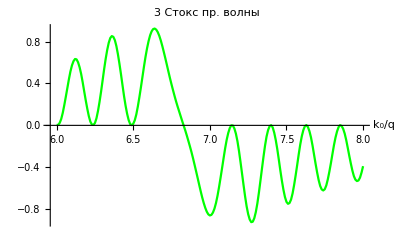
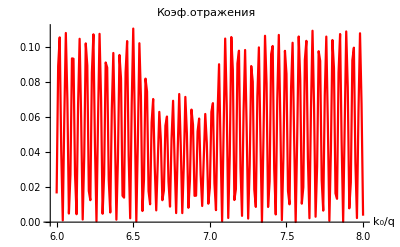
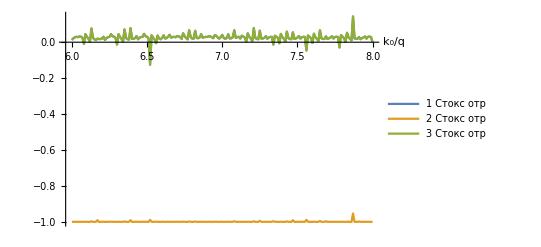
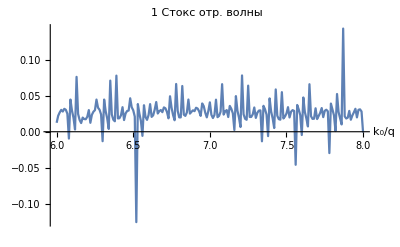

```mathematica
GetPlotsNormal[{1,0.5,0.01},{1,0},{6,8,0.01}]
```

При падении левополяризованного света, весь отраженный свет несет левую поляризацию. Но от щели отражается меньше, хотя пик заметен. Прошедший свет вне щели так же левый, а у щели эллиптический с пиком плоского света в центре щели. Однако левый свет отлично чувствует первую щель.

Материальные параметры: α=1, γ=0.5, β=0.01

Поляризация падающей волны: (правая)d+=0; (левая)d-=1

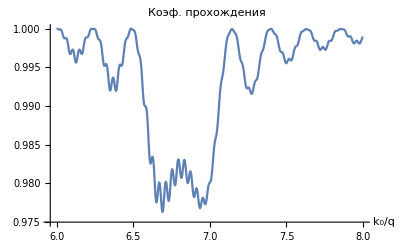
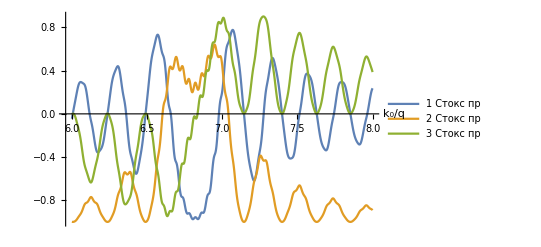
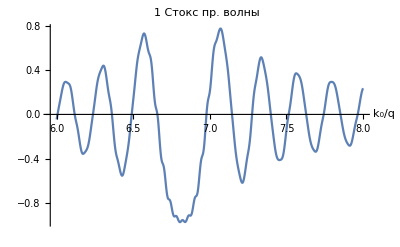
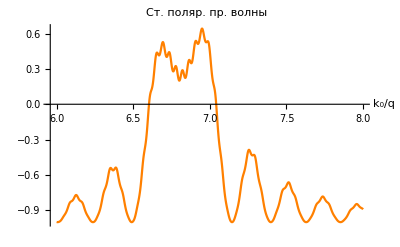
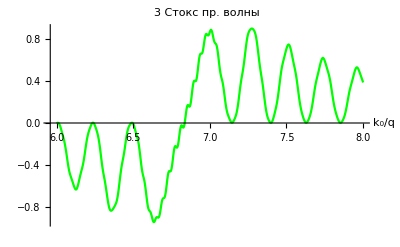
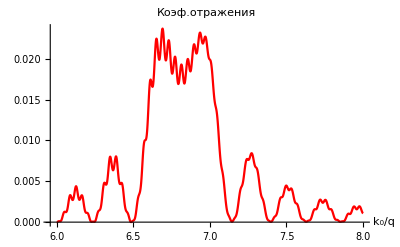
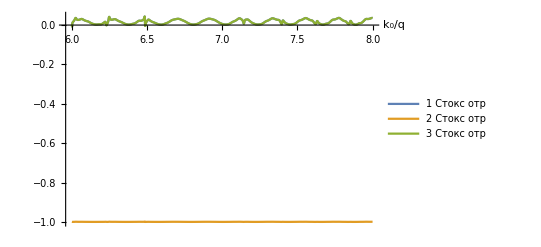
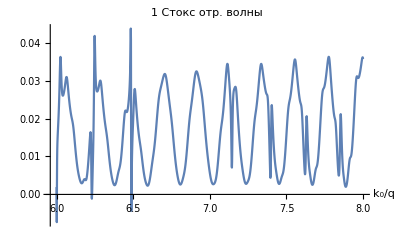

```mathematica
GetPlotsNormal[{1,0.5,0.01},{0,1},{6,8,0.001}]
```

!!
Из-за того, что первая щель мала, пик довольно узкий. Весь отраженный свет левый, прошедшей также левый, кроме области щели, где он слегка эллиптический.

Материальные параметры: α=1, γ=0.5, β=0.01

Поляризация падающей волны: (правая)d+=0; (левая)d-=1

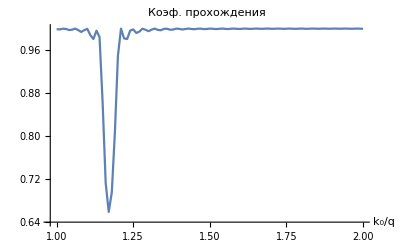
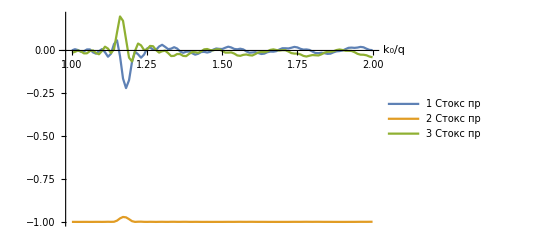
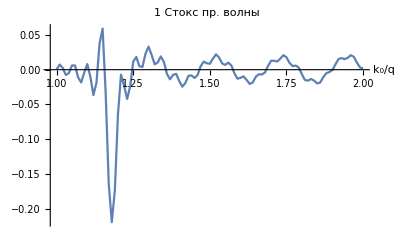
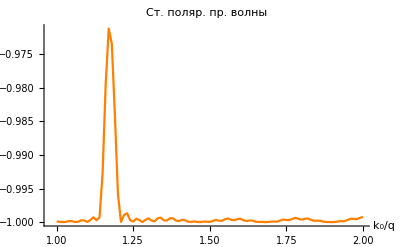
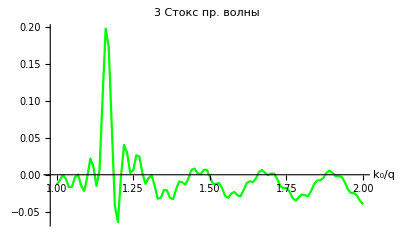
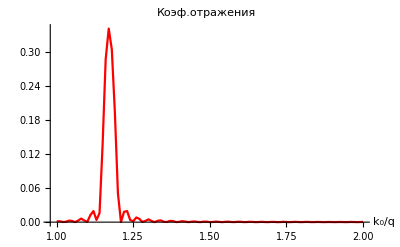
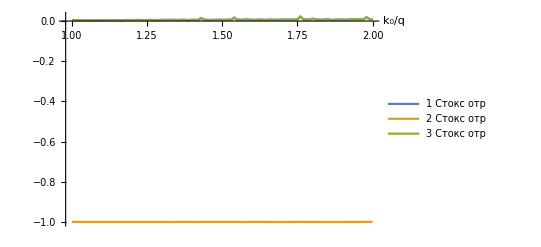
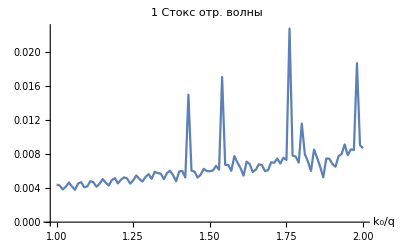

```mathematica
GetPlotsNormal[{1,0.5,0.01},{0,1},{1,2,0.01}]
```

При уменьшении величины щелей, вторая щель становится заметнее первой, однако в абсолютных значениях интенсивности ожидаемо падают. Поляризационные свойства качественно не изменяются.

Материальные параметры: α=1, γ=0.5, β=0.001

Поляризация падающей волны: (правая)d+=0; (левая)d-=1

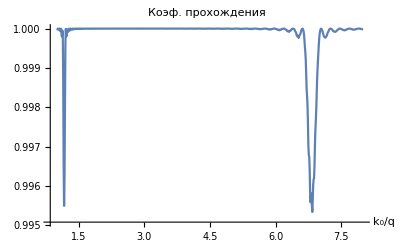
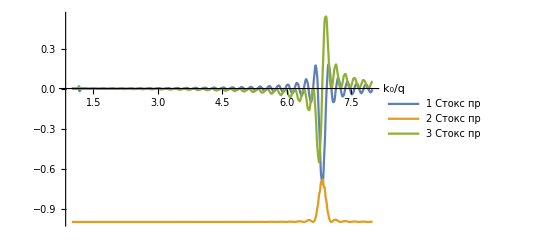
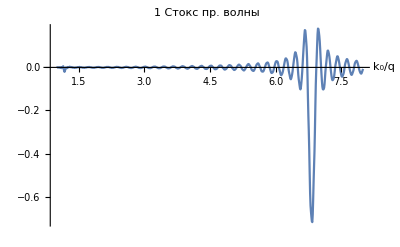
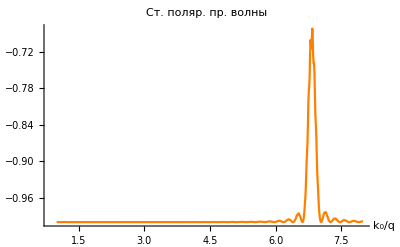
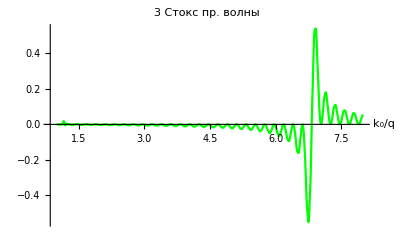
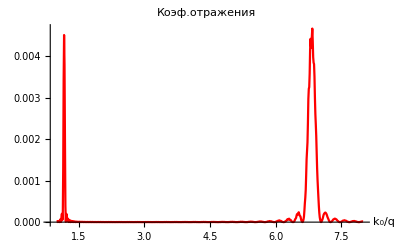
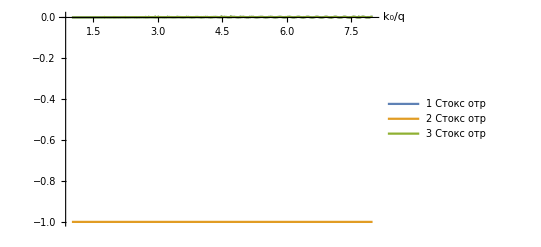
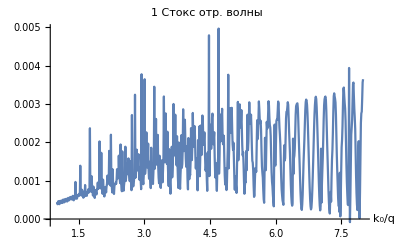

```mathematica
GetPlotsNormal[{1,0.5,0.001},{0,1},{1,8,0.01}]
```

В случае, когда закон дисперсии становится асимметричным в другую сторону, вторая щель отсутствует. А первая дает качественно те же результаты, что и чистый холестерик.

Материальные параметры: α=0.5, γ=1, β=0.01

Поляризация падающей волны: (правая)d+=0; (левая)d-=1

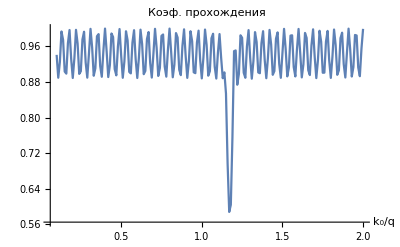
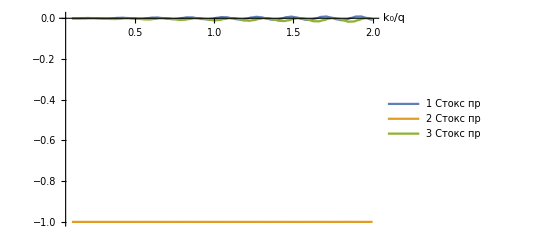
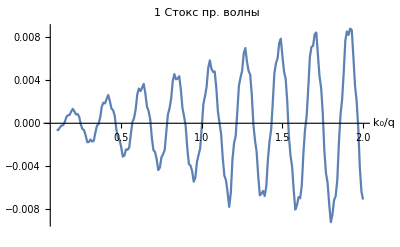
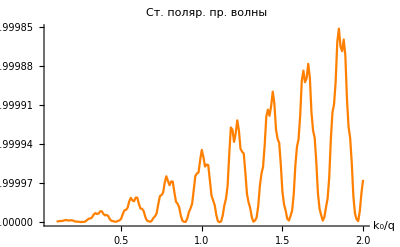
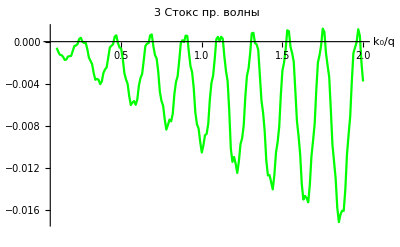
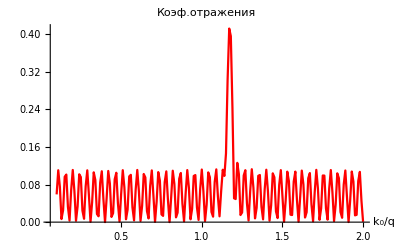
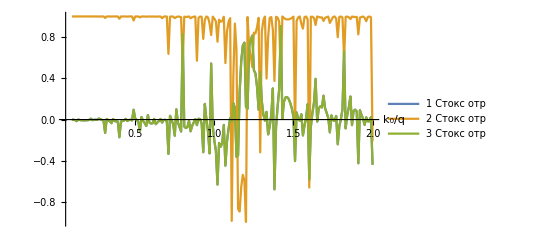
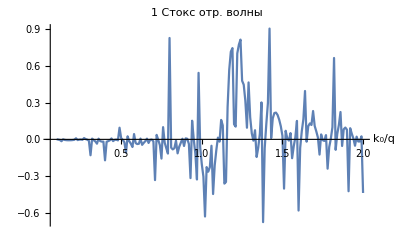

```mathematica
GetPlotsNormal[{0.5,1,0.01},{0,1},{0.1,2,0.01}]
```

Материальные параметры: α=1, γ=0.5, β=0.01

Поляризация падающей волны: (правая)d+=1; (левая)d-=1

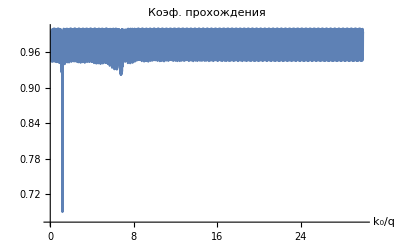
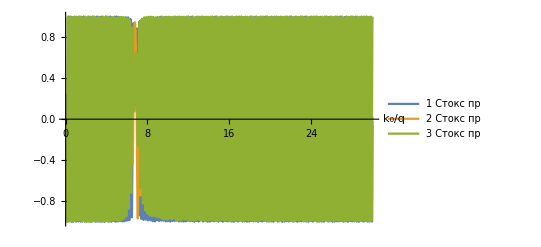
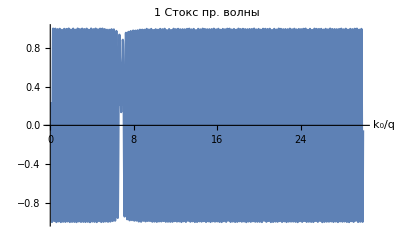
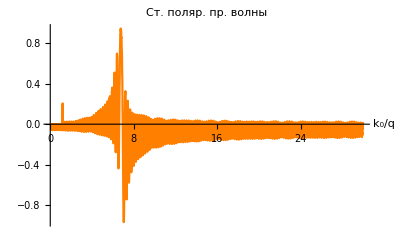
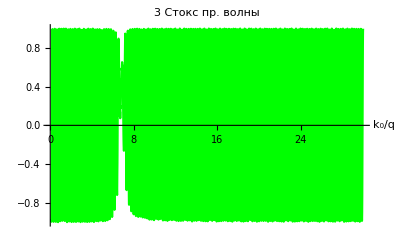
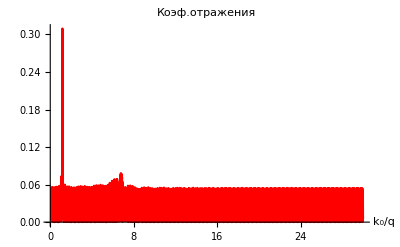
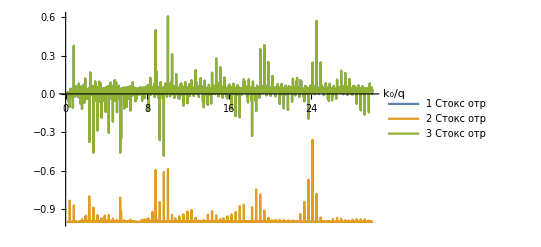
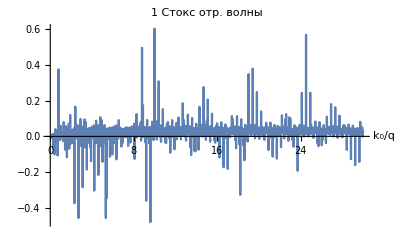

```mathematica
GetPlotsNormal[{1,0.5,0.01},{1,1},{0.1,30,0.01}]
```

Материальные параметры: α=1, γ=0.5, β=0.001

Поляризация падающей волны: (правая)d+=1; (левая)d-=1

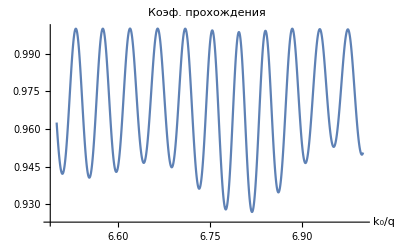
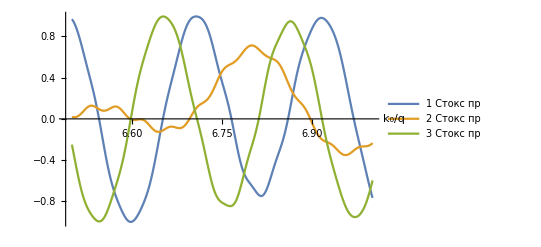
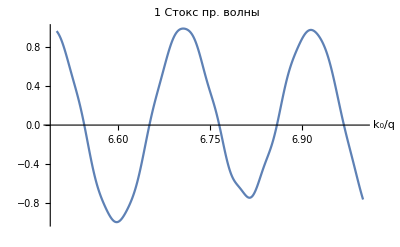
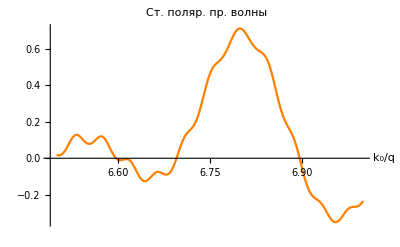
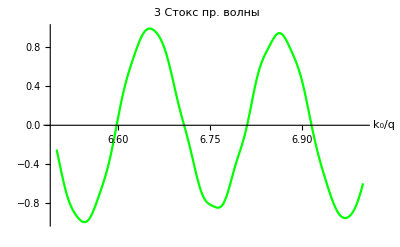
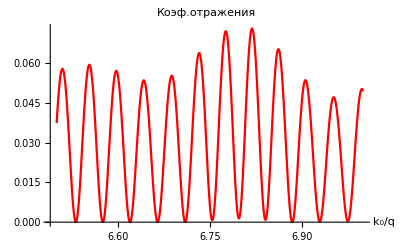
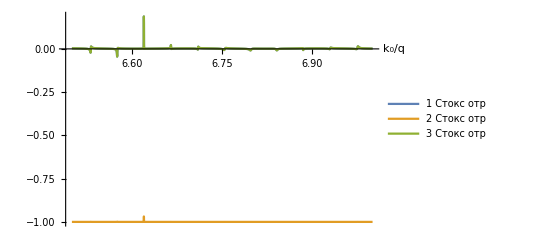
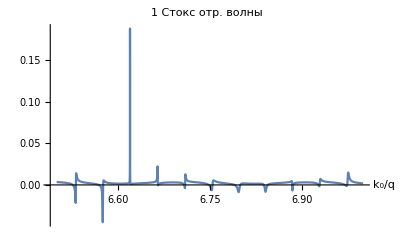

```mathematica
GetPlotsNormal[{1,0.5,0.001},{1,1},{6.5,7,0.0001}]
```

Материальные параметры: α=1, γ=0.5, β=0.001

Поляризация падающей волны: (правая)d+=1; (левая)d-=1

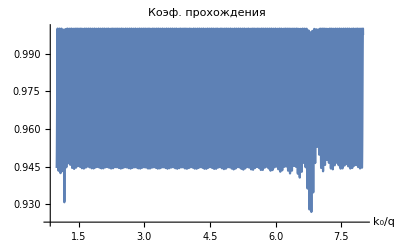
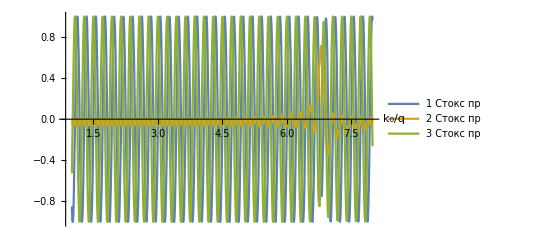
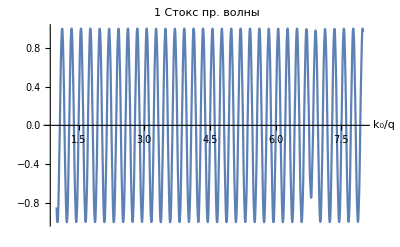
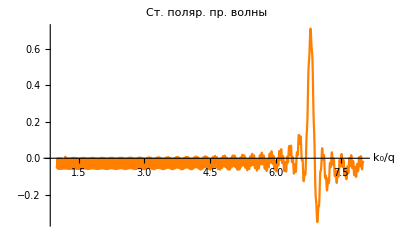
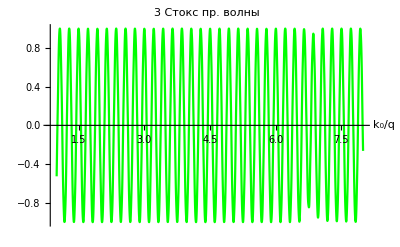
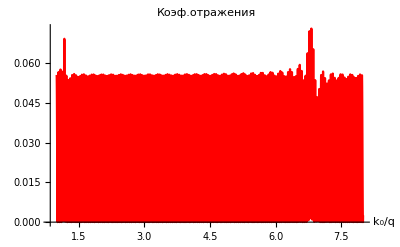
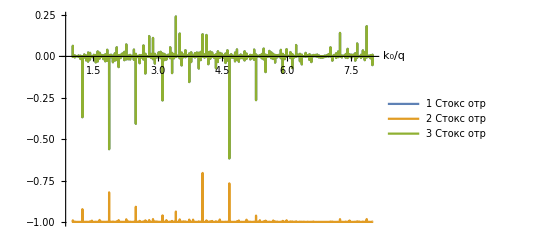
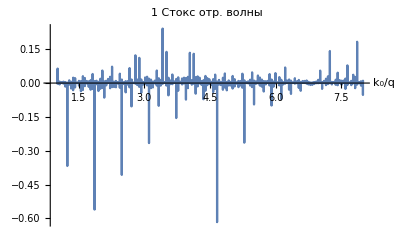

```mathematica
GetPlotsNormal[{1,0.5,0.001},{1,1},{1,8,0.001}]
```